вложение пыли - проверка формул для статьи

m                   - размерность объемлющего пространства
mmi               - число направлений объемлющего пространства с отрицательной сигнатурой (сначала положительные)
n                    - размерность поверхности
x[k]                - координаты x^μ
et[[a,b]]          - метрика объемлющего пространства η_ab
y[[a]]              - функция вложения y^a
e[[μ,a]]           - неквадратный репер e_μ^a
eo[[μ,a]]          - обратный неквадратный репер e_a^μ
g[[μ,ν]]            - метрика g_μν
go[[μ,ν]]          - обратная метрика g^μν
kr[[α,μ,ν]]       - символы Кристоффеля Γ_μν^α
krn[[α,μ,ν]]     - символы Кристоффеля с опущенным первым индексом Γ_(α,μν)
rim[[μ,ν,α,β]]  - тензор Римана R_μναβ
ric[[μ,ν]]         - тензор Ричи R_μν
rr                    - скалярная кривизна R
ein[[μ,ν]]         - тензор Эйнштейна G_μν
pr[[a,b]]          - проектор Π_b^a
po[[a,b]]          - ортогональный проектор (Π_(орт b))^a
b[[a,μ,ν]]         - вторая основная форма b_μν^a

функция взятия свертки тензора sp (списка) по значкам с номерами c1, c2

```mathematica
sv[sp_,c1_,c2_]:=Tr[Transpose[sp,Insert[Insert[Table[i,{i,3,Length[Dimensions[sp]]}],1,c1],2,c2]],Plus,2]
```

функция тензорного произведения

```mathematica
prt[ten1_,ten2_]:=Outer[Times,ten1,ten2]
```

функция тензорного произведения со сверткой

```mathematica
prts[ten1_,ten2_,c1_,c2_]:=sv[Outer[Times,ten1,ten2],c1,c2]
```

функция дифференцирования по координате (значок добавляется в начало)

```mathematica
dif[ten_]:=Table[D[ten,x[i]],{i,1,n}]
```

задание метрики

```mathematica
n=4;
```

```mathematica
ra=((9F[x[2]])/4)^(1/3)(ta0[x[2]]-x[1])^(2/3);
```

```mathematica
g={{1,0,0,0},{0,-D[ra,x[2]]^2,0,0},{0,0,-ra^2,0},{0,0,0,-ra^2 Sin[x[3]]^2}};
```

обратная метрика

```mathematica
go=Simplify[Inverse[g]]
```

{{1,0,0,0},{0,-(2 2^(1/3) 3^(2/3) F[x[2]]^(4/3) (ta0[x[2]]-x[1])^(2/3))/(ta0[x[2]] F'[x[2]]-x[1] F'[x[2]]+2 F[x[2]] ta0'[x[2]])^2,0,0},{0,0,-(2 (2/3)^(1/3))/(3 F[x[2]]^(2/3) (ta0[x[2]]-x[1])^(4/3)),0},{0,0,0,-(2 (2/3)^(1/3) Csc[x[3]]^2)/(3 F[x[2]]^(2/3) (ta0[x[2]]-x[1])^(4/3))}}

Кристоффель с нижним индексом

```mathematica
dg=dif[g];
krn=Simplify[(Transpose[dg,{2,3,1}]+Transpose[dg,{3,2,1}]-dg)/2];
```

Кристоффель с верхним индексом

```mathematica
kr=Simplify[prts[go,krn,2,3]];
```

тензор кривизны со всеми нижними индексами

```mathematica
rimns=Transpose[dif[kr],{3,1,2,4}]+Transpose[prts[kr,kr,2,4],{1,3,2,4}];
rim=Simplify[prts[g,(rimns-Transpose[rimns,{1,2,4,3}]),2,3]];
```

тензор Риччи с нижними индексами

```mathematica
ric=Simplify[sv[prts[go,rim,1,4],1,4]];
```

скалярная кривизна

```mathematica
rr=Simplify[sv[prts[go,ric,1,3],1,2]];
```

тензор Эйнштейна с нижними индексами

```mathematica
ein=Simplify[ric- g rr/2]
```

{{(4 F'[x[2]])/(3 (ta0[x[2]]-x[1]) (ta0[x[2]] F'[x[2]]-x[1] F'[x[2]]+2 F[x[2]] ta0'[x[2]])),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Det[g]
```

-9/4 (3/2)^(2/3) F[x[2]]^(4/3) Sin[x[3]]^2 (ta0[x[2]]-x[1])^(8/3) (((ta0[x[2]]-x[1])^(2/3) F'[x[2]])/(2^(2/3) 3^(1/3) F[x[2]]^(2/3))+((2/3)^(1/3) F[x[2]]^(1/3) ta0'[x[2]])/(ta0[x[2]]-x[1])^(1/3))^2

```mathematica
ko=FullSimplify[√(9/4 (3/2)^(2/3)) F[x[2]]^(2/3) (ta0[x[2]]-x[1])^(4/3) (((ta0[x[2]]-x[1])^(2/3) F'[x[2]])/(2^(2/3) 3^(1/3) F[x[2]]^(2/3))+((2/3)^(1/3) F[x[2]]^(1/3) ta0'[x[2]])/(ta0[x[2]]-x[1])^(1/3))]
```

3/4 (ta0[x[2]]-x[1]) ((ta0[x[2]]-x[1]) F'[x[2]]+2 F[x[2]] ta0'[x[2]])

```mathematica
FullSimplify[Det[g]/ko^2]
```

-Sin[x[3]]^2

```mathematica
FullSimplify[ein[[1,1]]ko]
```

F'[x[2]]

```mathematica
g//FullSimplify
```

{{1,0,0,0},{0,-((ta0[x[2]]-x[1]) F'[x[2]]+2 F[x[2]] ta0'[x[2]])^2/(2 2^(1/3) 3^(2/3) F[x[2]]^(4/3) (ta0[x[2]]-x[1])^(2/3)),0,0},{0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) (ta0[x[2]]-x[1])^(4/3),0},{0,0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) Sin[x[3]]^2 (ta0[x[2]]-x[1])^(4/3)}}

```mathematica
xv={x[1],ra,x[3],x[4]};
```

```mathematica
uu=dif[xv]
```

{{1,-((2/3)^(1/3) F[x[2]]^(1/3))/(ta0[x[2]]-x[1])^(1/3),0,0},{0,((ta0[x[2]]-x[1])^(2/3) F'[x[2]])/(2^(2/3) 3^(1/3) F[x[2]]^(2/3))+((2/3)^(1/3) F[x[2]]^(1/3) ta0'[x[2]])/(ta0[x[2]]-x[1])^(1/3),0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
gv=g;gv[[1,1]]=1-D[ra,x[1]]^2;gv[[1,2]]=D[ra,x[1]];gv[[2,1]]=D[ra,x[1]];gv[[2,2]]=-1;gv
```

{{1-((2/3)^(2/3) F[x[2]]^(2/3))/(ta0[x[2]]-x[1])^(2/3),-((2/3)^(1/3) F[x[2]]^(1/3))/(ta0[x[2]]-x[1])^(1/3),0,0},{-((2/3)^(1/3) F[x[2]]^(1/3))/(ta0[x[2]]-x[1])^(1/3),-1,0,0},{0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) (ta0[x[2]]-x[1])^(4/3),0},{0,0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) Sin[x[3]]^2 (ta0[x[2]]-x[1])^(4/3)}}

```mathematica
gn=prts[prts[uu,gv,2,3],uu,2,4]
```

{{1,0,0,0},{-((2/3)^(1/3) F[x[2]]^(1/3) (-((ta0[x[2]]-x[1])^(2/3) F'[x[2]])/(2^(2/3) 3^(1/3) F[x[2]]^(2/3))-((2/3)^(1/3) F[x[2]]^(1/3) ta0'[x[2]])/(ta0[x[2]]-x[1])^(1/3)))/(ta0[x[2]]-x[1])^(1/3)-((2/3)^(1/3) F[x[2]]^(1/3) (((ta0[x[2]]-x[1])^(2/3) F'[x[2]])/(2^(2/3) 3^(1/3) F[x[2]]^(2/3))+((2/3)^(1/3) F[x[2]]^(1/3) ta0'[x[2]])/(ta0[x[2]]-x[1])^(1/3)))/(ta0[x[2]]-x[1])^(1/3),(-((ta0[x[2]]-x[1])^(2/3) F'[x[2]])/(2^(2/3) 3^(1/3) F[x[2]]^(2/3))-((2/3)^(1/3) F[x[2]]^(1/3) ta0'[x[2]])/(ta0[x[2]]-x[1])^(1/3)) (((ta0[x[2]]-x[1])^(2/3) F'[x[2]])/(2^(2/3) 3^(1/3) F[x[2]]^(2/3))+((2/3)^(1/3) F[x[2]]^(1/3) ta0'[x[2]])/(ta0[x[2]]-x[1])^(1/3)),0,0},{0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) (ta0[x[2]]-x[1])^(4/3),0},{0,0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) Sin[x[3]]^2 (ta0[x[2]]-x[1])^(4/3)}}

```mathematica
gn-g//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
gv//FullSimplify
```

{{1-((2/3)^(2/3) F[x[2]]^(2/3))/(ta0[x[2]]-x[1])^(2/3),-((2/3)^(1/3) F[x[2]]^(1/3))/(ta0[x[2]]-x[1])^(1/3),0,0},{-((2/3)^(1/3) F[x[2]]^(1/3))/(ta0[x[2]]-x[1])^(1/3),-1,0,0},{0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) (ta0[x[2]]-x[1])^(4/3),0},{0,0,0,-3/2 (3/2)^(1/3) F[x[2]]^(2/3) Sin[x[3]]^2 (ta0[x[2]]-x[1])^(4/3)}}

```mathematica
ra
```

(3/2)^(2/3) F[x[2]]^(1/3) (ta0[x[2]]-x[1])^(2/3)

```mathematica
q1=Solve[ra==rn,x[1]]
```

{{x[1]→(-2 rn √(rn/F[x[2]]^(1/3))+3 F[x[2]]^(1/3) ta0[x[2]])/(3 F[x[2]]^(1/3))}}

```mathematica
FullSimplify[gv/.q1[[1,1]],F[x[2]]>0&&rn>0]
```

{{1-F[x[2]]/rn,-√(F[x[2]]/rn),0,0},{-√(F[x[2]]/rn),-1,0,0},{0,0,-rn^2,0},{0,0,0,-rn^2 Sin[x[3]]^2}}

```mathematica
g={{1-FF[x[1],x[2]]/x[2],-√(FF[x[1],x[2]]/x[2]),0,0},{-√(FF[x[1],x[2]]/x[2]),-1,0,0},{0,0,-x[2]^2,0},{0,0,0,-x[2]^2 Sin[x[3]]^2}};
```

обратная метрика

```mathematica
go=Simplify[Inverse[g]];
```

Кристоффель с нижним индексом

```mathematica
dg=dif[g];
krn=Simplify[(Transpose[dg,{2,3,1}]+Transpose[dg,{3,2,1}]-dg)/2];
```

Кристоффель с верхним индексом

```mathematica
kr=Simplify[prts[go,krn,2,3]];
```

тензор кривизны со всеми нижними индексами

```mathematica
rimns=Transpose[dif[kr],{3,1,2,4}]+Transpose[prts[kr,kr,2,4],{1,3,2,4}];
rim=Simplify[prts[g,(rimns-Transpose[rimns,{1,2,4,3}]),2,3]];
```

тензор Риччи с нижними индексами

```mathematica
ric=Simplify[sv[prts[go,rim,1,4],1,4]];
```

скалярная кривизна

```mathematica
rr=Simplify[sv[prts[go,ric,1,3],1,2]];
```

тензор Эйнштейна с нижними индексами

```mathematica
ein=Simplify[ric- g rr/2];
```

```mathematica
FF[x1_,x2_]:=(4 x2^3)/(9 x1^2)
```

```mathematica
FullSimplify[ein ,x[1]<0&&x[2]>0]
```

{{4/(3 x[1]^2),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
FullSimplify[ein √(-Det[g]),x[1]<0&&x[2]>0]
```

{{(4 √(Sin[x[3]]^2) x[2]^2)/(3 x[1]^2),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
√(-Det[g])
```

√(Sin[x[3]]^2 x[2]^4)

```mathematica
FF[x1_,x2_]:=FFF[x2^3/x1^2]
```

```mathematica
g
```

{{1-FFF[x[2]^3/x[1]^2]/x[2],-√(FFF[x[2]^3/x[1]^2]/x[2]),0,0},{-√(FFF[x[2]^3/x[1]^2]/x[2]),-1,0,0},{0,0,-x[2]^2,0},{0,0,0,-Sin[x[3]]^2 x[2]^2}}

```mathematica
g2={{1-FFF[x[2]^3/x[1]^2]/x[2],-√(FFF[x[2]^3/x[1]^2]/x[2])},{-√(FFF[x[2]^3/x[1]^2]/x[2]),0}}
```

{{1-FFF[x[2]^3/x[1]^2]/x[2],-√(FFF[x[2]^3/x[1]^2]/x[2])},{-√(FFF[x[2]^3/x[1]^2]/x[2]),0}}

```mathematica
xv={(-x[1])^(2/3),x[2]^3 x[1]^-2};
```

```mathematica
n=2;
```

```mathematica
uu=dif[xv]
```

{{-2/(3 (-x[1])^(1/3)),-(2 x[2]^3)/x[1]^3},{0,(3 x[2]^2)/x[1]^2}}

```mathematica
g2n=FullSimplify[Inverse[prts[prts[uu,Inverse[g2],1,3],uu,2,3]]/.{x[2]->t p^(1/3),x[1]->-t^(3/2)},t>0&&p>0]
```

{{(9 t)/4+3 p^(1/6) √FFF[p]-(9 FFF[p])/(4 p^(1/3)),(t √FFF[p])/(2 p^(5/6))},{(t √FFF[p])/(2 p^(5/6)),0}}

```mathematica
f[p_]:=3 p^(1/6) √FFF[p]-(9 FFF[p])/(4 p^(1/3));
h[p_]:=(√FFF[p])/(2 p^(5/6));
FFF[p_]:=Min[4/9 p,F0];
```

```mathematica
hi0=FullSimplify[Integrate[h[p],p]]
```

Piecewise[{{3 √F0 p^(1/6), 9 F0≤4 p}, {p^(2/3)/2, True}}]

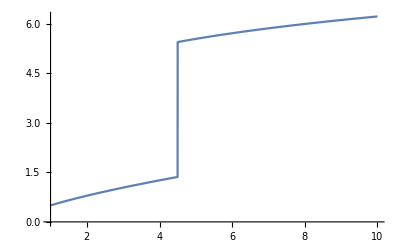

```mathematica
Plot[(hi0/.F0->2),{p,1,10}]
```

```mathematica
hi=FullSimplify[If[9 F0≤4 p,3 √F0 p^(1/6)-3 √F0 (9/4 F0)^(1/6)+(9/4 F0)^(2/3)/2,p^(2/3)/2]]
```

Piecewise[{{-9/4 (3/2)^(1/3) F0^(2/3)+3 √F0 p^(1/6), 9 F0≤4 p}, {p^(2/3)/2, True}}]

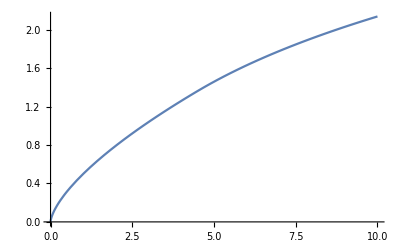

```mathematica
Plot[(hi/.F0->2),{p,0,10}]
```

```mathematica
FullSimplify[D[hi,p]-h[p]]
```

0

```mathematica
FullSimplify[1/(2 √6)f[p],p>0&&F0>0]
```

(3 p^(1/6) √Min[F0,(4 p)/9]-(9 Min[F0,(4 p)/9])/(4 p^(1/3)))/(2 √6)

```mathematica
1/(√6)hi
```

Piecewise[{{-9/4 (3/2)^(1/3) F0^(2/3)+3 √F0 p^(1/6), 9 F0≤4 p}, {p^(2/3)/2, True}}]/(√6)

```mathematica
FullSimplify[1/(√6)hi-1/(2 √6)f[p],p>0&&F0>0]
```

Piecewise[{{(√3 (3 F0+4 √(F0 p)+(F0^2 p)^(1/3) Root[324+#1^3&,1]))/(8 √2 p^(1/3)), 9 F0≤4 p}, {0, True}}]

```mathematica
N[Root[324+#1^3&,1]]
```

-6.86829

```mathematica
w[p_]:=HeavisideTheta[p-9/4 F0] 1/(√6)(-3/2 (9/4 F0)^(2/3)+9/8 F0 p^(-1/3)+p^(1/6)√(9/4 F0))
```

```mathematica
prov[pp_,FF_]:=((1/(√6)hi-1/(2 √6)f[p]-w[p])/.{p->pp,F0->FF})
```

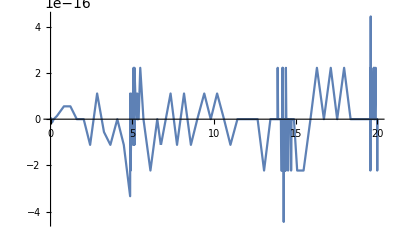

```mathematica
Plot[prov[pp,3],{pp,0,20}]
```

```mathematica
m=4;
mmi=2;
n=2;
y=Table[0,{a,1,m}];
y[[1]]=1/2((2 x[1]^3+9/8 x[1]^2+f[x[2]]x[1])+x[1]);
y[[2]]=w[x[2]];
y[[3]]=1/2((2 x[1]^3+9/8 x[1]^2+f[x[2]]x[1])-x[1]);
y[[4]]=√(3/2)x[1]^2-w[x[2]];
```

задание метрики объемлющего пространства

```mathematica
et=
Table[If[ a≠b,0,
If[a≤m-mmi,1,-1]],{a,1,m},{b,1,m}]
```

{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}}

вычисление репера

```mathematica
e=dif[y]//FullSimplify;
```

вычисление метрики

```mathematica
g=FullSimplify[prts[e,prts[e,et,2,3],2,4]]
```

{{(9 x[1])/4-(9 Min[F0,(4 x[2])/9])/(4 x[2]^(1/3))+3 √Min[F0,(4 x[2])/9] x[2]^(1/6),(Piecewise[{{(x[1] (3 F0+2 √F0 √x[2]))/(8 x[2]^(4/3)), 9 F0≤4 x[2]}, {x[1]/(3 x[2]^(1/3)), True}}])+√6 x[1] (2 √(2/3) DiracDelta[9 F0-4 x[2]] (-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0)/(8 x[2]^(1/3))+3/2 √F0 x[2]^(1/6))+(HeavisideTheta[-(9 F0)/4+x[2]] (-3 F0+2 √F0 √x[2]))/(8 √6 x[2]^(4/3)))},{(Piecewise[{{(x[1] (3 F0+2 √F0 √x[2]))/(8 x[2]^(4/3)), 9 F0≤4 x[2]}, {x[1]/(3 x[2]^(1/3)), True}}])-√6 x[1] (-2 √(2/3) DiracDelta[9 F0-4 x[2]] (-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0)/(8 x[2]^(1/3))+3/2 √F0 x[2]^(1/6))+(HeavisideTheta[-(9 F0)/4+x[2]] (3 F0-2 √F0 √x[2]))/(8 √6 x[2]^(4/3))),(-2 √(2/3) DiracDelta[9 F0-4 x[2]] (-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0)/(8 x[2]^(1/3))+3/2 √F0 x[2]^(1/6))+(HeavisideTheta[-(9 F0)/4+x[2]] (3 F0-2 √F0 √x[2]))/(8 √6 x[2]^(4/3))) (2 √(2/3) DiracDelta[9 F0-4 x[2]] (-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0)/(8 x[2]^(1/3))+3/2 √F0 x[2]^(1/6))+(HeavisideTheta[-(9 F0)/4+x[2]] (-3 F0+2 √F0 √x[2]))/(8 √6 x[2]^(4/3)))+(2 √(2/3) DiracDelta[9 F0-4 x[2]] (-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0)/(8 x[2]^(1/3))+3/2 √F0 x[2]^(1/6))+(HeavisideTheta[-(9 F0)/4+x[2]] (-3 F0+2 √F0 √x[2]))/(8 √6 x[2]^(4/3)))^2}}

```mathematica
FullSimplify[(g/.{x[1]->t,x[2]->p})-g2n,p>9/4 F0]
```

{{0,0},{0,0}}

```mathematica
FullSimplify[(g/.{x[1]->t,x[2]->p})-g2n,p<9/4 F0]
```

{{0,0},{0,0}}

```mathematica
Clear[f,w]
```

```mathematica
m=7;
mmi=5;
n=4;
y=Table[0,{a,1,m}];
y[[1]]=x[1]^2+9/16 x[1]^(4/3)+1/2 x[1]^(2/3)(f[x[2]^3/x[1]^2]+1);
y[[2]]=w[x[2]^3/x[1]^2];
y[[3]]=x[1]^2+9/16 x[1]^(4/3)+1/2 x[1]^(2/3)(f[x[2]^3/x[1]^2]-1);
y[[4]]=√(3/2)x[1]^(4/3)-w[x[2]^3/x[1]^2];
y[[5]]=x[2] Cos[x[3]];
y[[6]]=x[2] Sin[x[3]]Cos[x[4]];
y[[7]]=x[2] Sin[x[3]]Sin[x[4]];
```

задание метрики объемлющего пространства

```mathematica
et=
Table[If[ a≠b,0,
If[a≤m-mmi,1,-1]],{a,1,m},{b,1,m}]
```

{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,-1,0,0,0,0},{0,0,0,-1,0,0,0},{0,0,0,0,-1,0,0},{0,0,0,0,0,-1,0},{0,0,0,0,0,0,-1}}

вычисление репера

```mathematica
e=dif[y]//FullSimplify
```

dif[{1/2 (1+f[x[2]^3/x[1]^2]) x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2,w[x[2]^3/x[1]^2],1/2 (-1+f[x[2]^3/x[1]^2]) x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2,-w[x[2]^3/x[1]^2]+√(3/2) x[1]^(4/3),Cos[x[3]] x[2],Cos[x[4]] Sin[x[3]] x[2],Sin[x[3]] Sin[x[4]] x[2]}]

вычисление метрики

```mathematica
g=FullSimplify[prts[e,prts[e,et,2,3],2,4]]
```

prts[dif[{1/2 (1+f[x[2]^3/x[1]^2]) x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2,w[x[2]^3/x[1]^2],1/2 (-1+f[x[2]^3/x[1]^2]) x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2,-w[x[2]^3/x[1]^2]+√(3/2) x[1]^(4/3),Cos[x[3]] x[2],Cos[x[4]] Sin[x[3]] x[2],Sin[x[3]] Sin[x[4]] x[2]}],prts[dif[{1/2 (1+f[x[2]^3/x[1]^2]) x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2,w[x[2]^3/x[1]^2],1/2 (-1+f[x[2]^3/x[1]^2]) x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2,-w[x[2]^3/x[1]^2]+√(3/2) x[1]^(4/3),Cos[x[3]] x[2],Cos[x[4]] Sin[x[3]] x[2],Sin[x[3]] Sin[x[4]] x[2]}],{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,-1,0,0,0,0},{0,0,0,-1,0,0,0},{0,0,0,0,-1,0,0},{0,0,0,0,0,-1,0},{0,0,0,0,0,0,-1}},2,3],2,4]

```mathematica
f[p_]:=3 p^(1/6) √FFF[p]-(9 FFF[p])/(4 p^(1/3));
w[p_]:=HeavisideTheta[p-9/4 F0] 1/(√6)(-3/2 (9/4 F0)^(2/3)+9/8 F0 p^(-1/3)+p^(1/6)√(9/4 F0));
FFF[p_]:=Min[4/9 p,F0];
```

```mathematica
FullSimplify[g,x[1]>0&&x[2]>0&&(4 x[2]^3)/(9 x[1]^2)<F0]
```

prts[dif[{1/2 x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2+x[2]^2/(2 x[1]^(2/3)),0,-1/2 x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2+x[2]^2/(2 x[1]^(2/3)),√(3/2) x[1]^(4/3),Cos[x[3]] x[2],Cos[x[4]] Sin[x[3]] x[2],Sin[x[3]] Sin[x[4]] x[2]}],prts[dif[{1/2 x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2+x[2]^2/(2 x[1]^(2/3)),0,-1/2 x[1]^(2/3)+9/16 x[1]^(4/3)+x[1]^2+x[2]^2/(2 x[1]^(2/3)),√(3/2) x[1]^(4/3),Cos[x[3]] x[2],Cos[x[4]] Sin[x[3]] x[2],Sin[x[3]] Sin[x[4]] x[2]}],{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,-1,0,0,0,0},{0,0,0,-1,0,0,0},{0,0,0,0,-1,0,0},{0,0,0,0,0,-1,0},{0,0,0,0,0,0,-1}},2,3],2,4]

```mathematica
FullSimplify[g,x[1]>0&&x[2]>0&&(4 x[2]^3)/(9 x[1]^2)>F0]
```

prts[dif[{1/16 x[1]^(1/3) (8 x[1]^(1/3)+16 x[1]^(5/3)+x[1] (9-(18 F0)/x[2])+24 √(F0 x[2])),(-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0 x[1]^(2/3))/(8 x[2])+(3 √(F0 x[2]))/(2 x[1]^(1/3)))/(√6),1/16 x[1]^(1/3) (-8 x[1]^(1/3)+16 x[1]^(5/3)+x[1] (9-(18 F0)/x[2])+24 √(F0 x[2])),(9/4 (3/2)^(1/3) F0^(2/3)+3 x[1]^(4/3)-(9 F0 x[1]^(2/3))/(8 x[2])-(3 √(F0 x[2]))/(2 x[1]^(1/3)))/(√6),Cos[x[3]] x[2],Cos[x[4]] Sin[x[3]] x[2],Sin[x[3]] Sin[x[4]] x[2]}],prts[dif[{1/16 x[1]^(1/3) (8 x[1]^(1/3)+16 x[1]^(5/3)+x[1] (9-(18 F0)/x[2])+24 √(F0 x[2])),(-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0 x[1]^(2/3))/(8 x[2])+(3 √(F0 x[2]))/(2 x[1]^(1/3)))/(√6),1/16 x[1]^(1/3) (-8 x[1]^(1/3)+16 x[1]^(5/3)+x[1] (9-(18 F0)/x[2])+24 √(F0 x[2])),(9/4 (3/2)^(1/3) F0^(2/3)+3 x[1]^(4/3)-(9 F0 x[1]^(2/3))/(8 x[2])-(3 √(F0 x[2]))/(2 x[1]^(1/3)))/(√6),Cos[x[3]] x[2],Cos[x[4]] Sin[x[3]] x[2],Sin[x[3]] Sin[x[4]] x[2]}],{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,-1,0,0,0,0},{0,0,0,-1,0,0,0},{0,0,0,0,-1,0,0},{0,0,0,0,0,-1,0},{0,0,0,0,0,0,-1}},2,3],2,4]

проверка гладкости

```mathematica
f[p]
```

3 p^(1/6) √Min[F0,(4 p)/9]-(9 Min[F0,(4 p)/9])/(4 p^(1/3))

```mathematica
Simplify[f[p],p<9/4 F0]
```

p^(2/3)

```mathematica
Simplify[f[p],p<9/4 F0]/.p->9/4 F0
```

3/2 (3/2)^(1/3) F0^(2/3)

```mathematica
Simplify[f[p],p>9/4 F0]/.p->9/4 F0
```

3/2 (3/2)^(1/3) F0^(2/3)

```mathematica
Simplify[D[f[p],p],p<9/4 F0]/.p->9/4 F0
```

(2 (2/3)^(2/3))/(3 F0^(1/3))

```mathematica
Simplify[D[f[p],p],p>9/4 F0]/.p->9/4 F0
```

(2 (2/3)^(2/3))/(3 F0^(1/3))

```mathematica
Simplify[D[f[p],{p,2}],p<9/4 F0]/.p->9/4 F0
```

-(8 (2/3)^(2/3))/(81 F0^(4/3))

```mathematica
Simplify[D[f[p],{p,2}],p>9/4 F0]/.p->9/4 F0
```

-(26 (2/3)^(2/3))/(81 F0^(4/3))

```mathematica
w[p]
```

((-9/4 (3/2)^(1/3) F0^(2/3)+(9 F0)/(8 p^(1/3))+3/2 √F0 p^(1/6)) HeavisideTheta[-(9 F0)/4+p])/(√6)

```mathematica
Simplify[w[p],p>9/4 F0]/.p->9/4 F0
```

0

```mathematica
Simplify[D[w[p],p],p>9/4 F0]/.p->9/4 F0
```

0

```mathematica
Simplify[D[w[p],{p,2}],p>9/4 F0]/.p->9/4 F0
```

(2/3)^(1/6)/(81 F0^(4/3))

```mathematica
F0=1;
```

```mathematica
f[p]
```

3 p^(1/6) √Min[1,(4 p)/9]-(9 Min[1,(4 p)/9])/(4 p^(1/3))

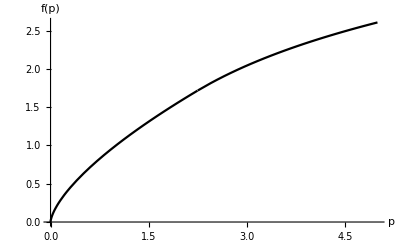

```mathematica
Plot[f[p],{p,0,5},AxesLabel->{"p","f(p)"},PlotStyle->Black,AxesStyle->Directive[Black,16]]
```

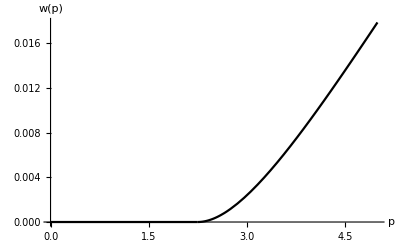

```mathematica
Plot[w[p],{p,0,5},AxesLabel->{"p","w(p)"},PlotStyle->Black,AxesStyle->Directive[Black,16]]
```

```mathematica
cvet={{Green,Blue,Red},{GrayLevel[0.7],GrayLevel[0.5],GrayLevel[0.3]}}
```

{{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{GrayLevel[0.7],GrayLevel[0.5],GrayLevel[0.3]}}

```mathematica
F0=1;
y145={y[[1]],y[[4]],r}/.{x[1]->t,x[2]->Abs[r]}
```

{(9 t^(4/3))/16+t^2+1/2 t^(2/3) (1+3 (1/t^2)^(1/6) √Abs[r] √Min[1,(4 Abs[r]^3)/(9 t^2)]-(9 Min[1,(4 Abs[r]^3)/(9 t^2)])/(4 (1/t^2)^(1/3) Abs[r])),√(3/2) t^(4/3)-((-9/4 (3/2)^(1/3)+9/(8 (1/t^2)^(1/3) Abs[r])+3/2 (1/t^2)^(1/6) √Abs[r]) HeavisideTheta[-9/4+Abs[r]^3/t^2])/(√6),r}

```mathematica
cv=1;
ParametricPlot3D[y145/.t->Exp[tt],{tt,-6,1},{r,-5,5},ColorFunction->Function[{x,y,z,tt,r},If[4 Abs[r]^3<9F0 Exp[tt]^2&&Exp[tt]<2/3 F0,cvet[[cv,3]],If[4 Abs[r]^3<9F0 Exp[tt]^2,cvet[[cv,2]],cvet[[cv,1]]]]],ColorFunctionScaling->False,RegionFunction->Function[{x,y,z,tt,r},0<x<8&&-5<y<5],PlotPoints->100,Axes->True,Boxed->False,AxesLabel->{"y^0","y^3","y^4"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

```mathematica
Export["file2.eps",-Graphics3D-,AllowRasterization->False]
```

file2.eps

```mathematica
m=6;
mmi=5;
n=4;
y=Table[0,{a,1,m}];
y[[1]]=x[1]^2+9/16 x[1]^(4/3)+1/2 x[1]^(2/3);
y[[2]]=x[1]^2+9/16 x[1]^(4/3)-1/2 x[1]^(2/3);
y[[3]]=√(3/2)x[1]^(4/3);
y[[4]]=x[2] Cos[x[3]];
y[[5]]=x[2] Sin[x[3]]Cos[x[4]];
y[[6]]=x[2] Sin[x[3]]Sin[x[4]];
```

задание метрики объемлющего пространства

```mathematica
et=
Table[If[ a≠b,0,
If[a≤m-mmi,1,-1]],{a,1,m},{b,1,m}]
```

{{1,0,0,0,0,0},{0,-1,0,0,0,0},{0,0,-1,0,0,0},{0,0,0,-1,0,0},{0,0,0,0,-1,0},{0,0,0,0,0,-1}}

вычисление репера

```mathematica
e=dif[y]//FullSimplify
```

{{1/(3 x[1]^(1/3))+3/4 x[1]^(1/3)+2 x[1],-1/(3 x[1]^(1/3))+3/4 x[1]^(1/3)+2 x[1],2 √(2/3) x[1]^(1/3),0,0,0},{0,0,0,Cos[x[3]],Cos[x[4]] Sin[x[3]],Sin[x[3]] Sin[x[4]]},{0,0,0,-Sin[x[3]] x[2],Cos[x[3]] Cos[x[4]] x[2],Cos[x[3]] Sin[x[4]] x[2]},{0,0,0,0,-Sin[x[3]] Sin[x[4]] x[2],Cos[x[4]] Sin[x[3]] x[2]}}

вычисление метрики

```mathematica
g=FullSimplify[prts[e,prts[e,et,2,3],2,4]]
```

{{1,0,0,0},{0,-1,0,0},{0,0,-x[2]^2,0},{0,0,0,-Sin[x[3]]^2 x[2]^2}}

обратная метрика

```mathematica
go=Simplify[Inverse[g]]
```

{{1,0,0,0},{0,-1,0,0},{0,0,-1/x[2]^2,0},{0,0,0,-Csc[x[3]]^2/x[2]^2}}

Кристоффель с нижним индексом

```mathematica
dg=dif[g];
krn=Simplify[(Transpose[dg,{2,3,1}]+Transpose[dg,{3,2,1}]-dg)/2];
```

Кристоффель с верхним индексом

```mathematica
kr=Simplify[prts[go,krn,2,3]];
```

тензор кривизны со всеми нижними индексами

```mathematica
rimns=Transpose[dif[kr],{3,1,2,4}]+Transpose[prts[kr,kr,2,4],{1,3,2,4}];
rim=Simplify[prts[g,(rimns-Transpose[rimns,{1,2,4,3}]),2,3]]
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

```mathematica
F0=0;
y135={y[[1]],y[[3]],r}/.{x[1]->t,x[2]->Abs[r]}
```

{t^(2/3)/2+(9 t^(4/3))/16+t^2,√(3/2) t^(4/3),r}

```mathematica
cv=1;
ParametricPlot3D[y135/.t->Exp[tt],{tt,-6,1},{r,-5,5},ColorFunction->Function[{x,y,z,tt,r},If[4 Abs[r]^3<9F0 Exp[tt]^2&&Exp[tt]<2/3 F0,cvet[[cv,3]],If[4 Abs[r]^3<9F0 Exp[tt]^2,cvet[[cv,2]],cvet[[cv,1]]]]],ColorFunctionScaling->False,RegionFunction->Function[{x,y,z,tt,r},0<x<8&&-5<y<5],PlotPoints->100,Axes->True,Boxed->False,AxesLabel->{"y^0","y^3","y^4"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-